GammaDistribution[3,1]

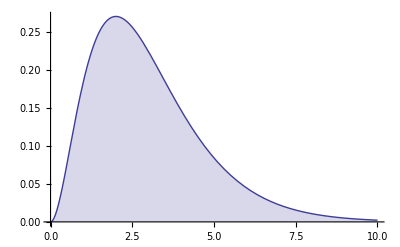

```mathematica
Γ=GammaDistribution[3,1]
Plot[PDF[Γ,x],{x,0,10}, Filling->Axis]
```

```mathematica
Manipulate[
Γ=GammaDistribution[k,λ];
Plot[SurvivalFunction[Γ,x],{x,0,10},Filling->Axis],
{{k,3},0,5},{{λ,1}, 1,3}]
```

```mathematica
Γ=GammaDistribution[k,λ];
Integrate[SurvivalFunction[Γ,x],
{x,0,∞},Assumptions->{k>0, λ>0}]
```

k λ

```mathematica
𝒩=NormalDistribution[μ,σ];
Integrate[SurvivalFunction[𝒩,x],{x,0,∞},Assumptions->σ>0]
```

1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])